## Yukawa model

We implement here a Yukawa theory, more explicitly a quark-meson model, which is a low-energy effective theory of QCD.

## Setup

```mathematica
Get["FunKit`"]
```

Mathematica package TensorBases loaded

Authors: Andreas Geißel, Franz Richard Sattler

Version: 1.0

Year: 2025

For a list of available bases, call TBInfo[]. For further information on a particular basis, call TBInfo["BasisName"].

This package provides the methods TBGetBasisElement, TBGetInnerProduct, TBGetMetric, TBGetInverseMetric, TBGetProjector for every tensor basis available.

For closer explanations, please call their usage messages, e.g. TBGetProjector::usage.

Other useful tools include TBBasisTransformation, TBVertexTransformation, TBGetIdentityMatrix, TBGetBasisSize, TBGetIndexSet, TBMakePropagator.

To build or manipulate bases, please call TBInfo["BaseBuilder"].

To show information on the used notation, call TBInfo["Notation"].

FormTracer package already loaded.

Clearing all extra variables for compatibility!

To see all (user-defined and package-defined) FormTracer definitions, call TBInfo["FormTracer"].

Furthermore, TensorBases extends FormTracer. To see all extensions, call TBInfo["Extensions"]

To see all momentum transformations that can be performed by TensorBases, call TBInfo["Momenta"].

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0.0
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

The mesons sigma and pi are commuting fields; the quarks psi and psibar are Grassmann fields. The truncation lists the meson self-interactions, the quark two-point function, and the two Yukawa vertices. We envisage here an interation as ψ̄(σ+ⅈ γ_5 τ π)ψ
We also allow for σ to have a finite expectation value.

```mathematica
fields = <|
    "Commuting" -> {σ[p], Π[p, {f}]},
    "Grassmann" -> {{Psibar[p, {a}], Psi[p, {a}]}}
|>;

truncation = <|
    GammaN -> {
        (* meson 2-point *)
        {σ, σ}, {Π, Π},
        (* quark 2-point *)
        {Psi, Psibar},
        (* meson 3-point *)
        {σ, σ, σ}, {σ, Π, Π},
        (* meson 4-point *)
        {σ, σ, σ, σ}, {Π, Π, Π, Π}, {σ, σ, Π, Π},
        (* Yukawa vertices: {Psi, Psibar, boson} *)
        {Psi, Psibar, σ}, {Psi, Psibar, Π}
    },
    Propagator -> {{σ, σ}, {Π, Π}, {Psi, Psibar}},
    Rdot -> {{σ, σ}, {Π, Π}, {Psi, Psibar}},
    Field -> {{σ}},
    S -> {
        (* meson 2-point *)
        {σ, σ}, {Π, Π},
        (* quark 2-point *)
        {Psi, Psibar},
        (* Yukawa vertices: {Psi, Psibar, boson} *)
        {Psi, Psibar, σ}, {Psi, Psibar, Π}
    }
|>;

setup = <|"FieldSpace" -> fields, "Truncation" -> truncation|>;
FSetGlobalSetup[setup];

FSetTexStyles[
    σ -> "\\sigma",
    Π -> "\\pi",
    Psi -> "\\psi",
    Psibar -> "\\bar{\\psi}"
];
```

## fRG: Two-point functions


-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

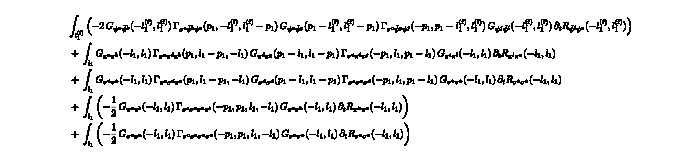

```mathematica
fRGSigma2P=FTakeDerivatives[WetterichEquation,{σ[i1],σ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

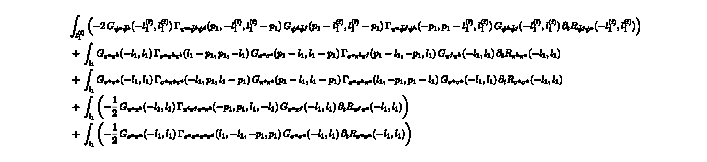

```mathematica
fRGPi2P=FTakeDerivatives[WetterichEquation,{Π[i1], Π[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

Quark two-point flow equation. The derivative list uses the {Psi, Psibar} ordering of the truncation.

-Graphics-+-Graphics-+-Graphics-+-Graphics-

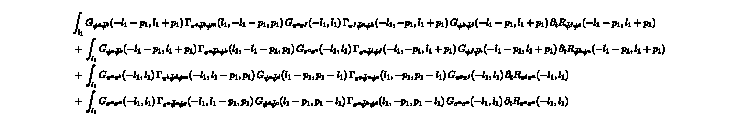

```mathematica
fRGQuark2P=FTakeDerivatives[WetterichEquation,{Psi[i1],Psibar[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

## fRG: Three-point functions

```mathematica
fRGYukawaSigma=FTakeDerivatives[WetterichEquation,{Psibar[i1],Psi[i2],σ[i3]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRGYukawaPi=FTakeDerivatives[WetterichEquation,{Psibar[i1],Psi[i2],Π[i3]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## DSE: Two-point functions


-Graphics-+-Graphics-

-Graphics-

```mathematica
DSESigma2P=FTakeDerivatives[FMakeDSE[σ[i2]],{σ[i1]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
DSEPi2P=FTakeDerivatives[FMakeDSE[Π[i2]], {Π[i1]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-

-Graphics-

Quark two-point flow equation. The derivative list uses the {Psi, Psibar} ordering of the truncation.

```mathematica
DSEQuark2P=FTakeDerivatives[FMakeDSE[Psi[i2]],{Psibar[i1]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-

-Graphics-

## DSE: Three-point functions

```mathematica
DSEYukawaSigma=FTakeDerivatives[FMakeDSE[σ[i3]],{Psibar[i1],Psi[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-

-Graphics-

```mathematica
fRGYukawaPi=FTakeDerivatives[FMakeDSE[Π[i3]],{Psibar[i1],Psi[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-

-Graphics-